```mathematica
real={0.96528, 0.0149123,
1.25157, 0.00845682,
1.54737, 0.00526321,
1.84514, 0.00275424,
2.18853, 0.00138275,
2.58641, 0.000439269,
2.985, 0.000131974,
3.384, 0.0000434909,
3.78326 ,0.0000160664,
4.39523 ,0.00000190021};
```

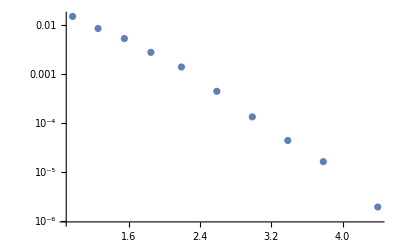

```mathematica
realplot=ListLogPlot[Table[{real[[2i-1]],real[[2i]]},{i,1,10}]]
```

reverse slope T=0.249,Ts=0.327,cS=11.537,cT=37.2739,error=  0.79

```mathematica
Import@SystemDialogInput["FileOpen"]
```

%pt           TTT           TTS           TSS           TSS2j           SSS           SSS2j           Tot
        0.965    1.43389E-02    2.89324E-19    2.08494E-19    5.83784E-37    1.50247E-19    4.20690E-37    1.43389E-02
        1.252    9.28431E-03    1.93445E-19    1.43949E-19    4.03057E-37    1.07117E-19    2.99928E-37    9.28431E-03
        1.547    5.26542E-03    1.19965E-19    9.76155E-20    2.73323E-37    7.94297E-20    2.22403E-37    5.26542E-03
        1.845    2.75556E-03    7.13217E-20    6.59288E-20    1.84601E-37    6.09437E-20    1.70642E-37    2.75556E-03
        2.189    1.22634E-03    3.79768E-20    4.20020E-20    1.17606E-37    4.61219E-20    1.30070E-37    1.22634E-03
        2.586    4.53661E-04    1.78336E-20    2.50374E-20    7.01048E-38    3.43979E-20    9.84233E-38    4.53661E-04
        2.985    1.60758E-04    8.22036E-21    1.50125E-20    4.20349E-38    2.64374E-20    7.67664E-38    1.60758E-04
        3.384    5.52794E-05    3.74486E-21    8.96339E-21    2.53693E-38    2.08252E-20    6.07219E-38    5.52794E-05
        3.783    1.85962E-05    1.69284E-21    5.40537E-21    1.54102E-38    1.67428E-20    4.92059E-38    1.85962E-05
        4.395    3.39755E-06    4.96780E-22    2.51083E-21    7.26379E-39    1.23859E-20    3.67126E-38    3.39755E-06

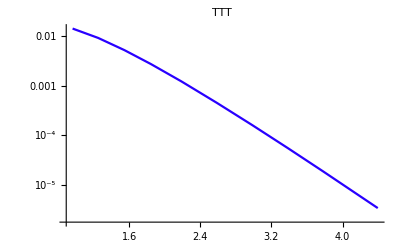
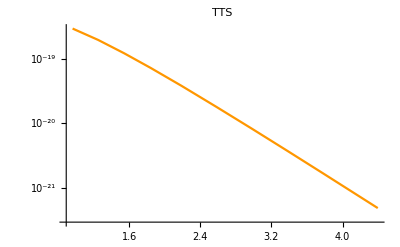
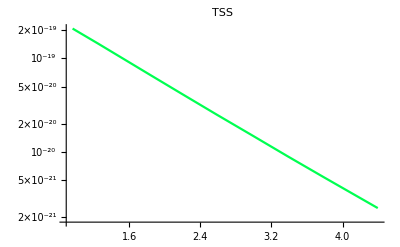
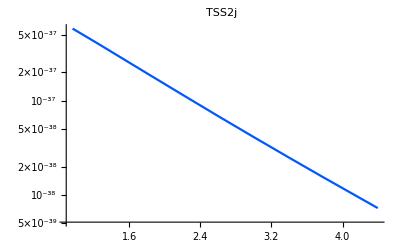
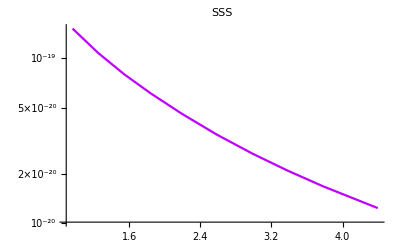
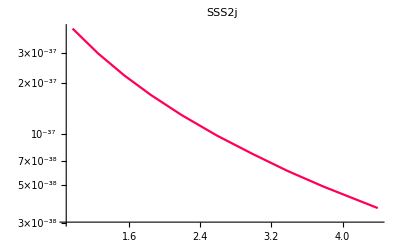
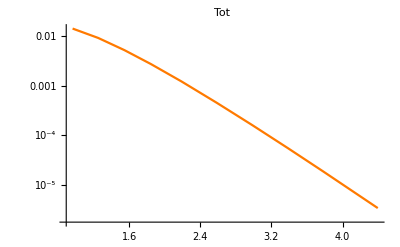

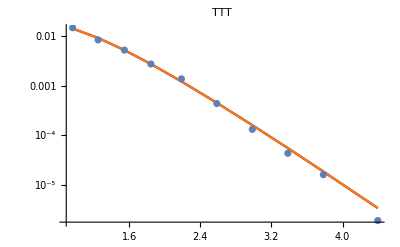

```mathematica
datalabel=StringSplit[StringTrim[StringSplit[%,"\n"][[1]]]];
datalist=StringReplace[#,"E"->"*10^"]&/@ StringSplit[#,"    "]&/@StringSplit[%%,"\n"][[2;;11]]//ToExpression;
Table[ListLogPlot[Join[Partition[datalist[[All,1]],1],Partition[datalist[[All,i]],1],2],PlotLabel->Style[datalabel[[i]],Hue[N@Log[i]]],Joined->True,PlotStyle->Hue[Log@i],PlotRange->Full],{i,2,8}]
Show[{%,realplot}]
```

```mathematica
Export["Omega.eps",#]
```

Omega.eps